```mathematica
Clear[pp,dez]
bin[z_,k_]:=bin[z,k]=Product[z-j,{j,0,k-1}]/k!
FI[n_]:=FactorInteger[n];FI[1]:={}
bin[z_,k_]:=bin[z,k]=Product[z-j,{j,0,k-1}]/k!
pp[n_,s_,k_]:=pp[n,s,k]=Sum[ m^(-s j) pp[n-j,s,k-1],{j,1,n-1}]
pp[n_,s_,1]:=m^(-s n)
pp[n_,s_,0]:=If[n==0,1,0]
pss[n_,s_,z_]:=Sum[ bin[z,k] pp[n,s,k],{k,0,n}]
pass[n_,s_,z_]:=Sum[pss[j,s,z],{j,1,n}]
dez[n_,z_]:=Product[z^p[[2]] /(p[[2]]!),{p,FI[n]}]
```

```mathematica
Expand@Table[D[pss[n,-1,z],z]/.z->0,{n,1,10}]
```

{m,m^2/2,m^3/3,m^4/4,m^5/5,m^6/6,m^7/7,m^8/8,m^9/9,m^10/10}

```mathematica
Table[pss[n,-s,3],{n,1,10}]
```

{3 m^s,6 m^(2 s),10 m^(3 s),15 m^(4 s),21 m^(5 s),28 m^(6 s),36 m^(7 s),45 m^(8 s),55 m^(9 s),66 m^(10 s)}

```mathematica
FullSimplify@Table[pss[n,s,z],{n,1,10}]//TableForm
```

m^-s z
1/2 m^(-2 s) z (1+z)
1/6 m^(-3 s) z (1+z) (2+z)
1/24 m^(-4 s) z (1+z) (2+z) (3+z)
1/120 m^(-5 s) z (1+z) (2+z) (3+z) (4+z)
1/720 m^(-6 s) z (1+z) (2+z) (3+z) (4+z) (5+z)
(m^(-7 s) z (1+z) (2+z) (3+z) (4+z) (5+z) (6+z))/5040
(m^(-8 s) z (1+z) (2+z) (3+z) (4+z) (5+z) (6+z) (7+z))/40320
(m^(-9 s) z (1+z) (2+z) (3+z) (4+z) (5+z) (6+z) (7+z) (8+z))/362880
(m^(-10 s) z (1+z) (2+z) (3+z) (4+z) (5+z) (6+z) (7+z) (8+z) (9+z))/3628800

```mathematica
Sum[ Binomial[z,k],{k,0,Infinity}]
```

2^z

```mathematica
Sum[ Binomial[z,k] x^(-s k),{k,0,Infinity}]
```

(1+x^-s)^z

```mathematica
Sum[ Pochhammer[z,k]/k!  x^(-s k),{k,0,Infinity}]
```

(1-x^-s)^-z

```mathematica
Sum[ z^k/k!  x^(-s k),{k,0,Infinity}]
```

ⅇ^(x^-s z)

```mathematica
Sum[ Pochhammer[z,k]/k!  x^(-s k),{k,0,Infinity}]
```

(1-x^-s)^-z

```mathematica
(1-x^-s)^-z/.x->5/.z->1/.s->2
```

25/24

```mathematica
Sum[ z^k/k!  x^(-s k),{k,0,Infinity}]
```

ⅇ^(x^-s z)

```mathematica
ⅇ^(x^-s z)/.z->1/.x->5/.s->2
```

ⅇ^(1/25)

```mathematica
N@Product[ E^(1/Prime[j]^2),{j,1,100000}]
```

1.57184

```mathematica
N@Pi^2/6
```

1.64493

```mathematica
N@Product[ E^(1/Prime[j]^2),{j,1,1000000}]
```

$Aborted

```mathematica
N@Product[ E^(1/Prime[j]^3),{j,1,100000}]
```

1.19096

```mathematica
Table[N@Pi^3/n,{n,1,50}]
```

{31.0063,15.5031,10.3354,7.75157,6.20126,5.16771,4.42947,3.87578,3.44514,3.10063,2.81875,2.58386,2.3851,2.21473,2.06709,1.93789,1.8239,1.72257,1.63191,1.55031,1.47649,1.40938,1.3481,1.29193,1.24025,1.19255,1.14838,1.10737,1.06918,1.03354,1.0002,0.968946,0.939584,0.911949,0.885894,0.861285,0.838007,0.815955,0.795033,0.775157,0.756251,0.738245,0.721076,0.704688,0.689028,0.674049,0.659708,0.645964,0.632781,0.620126}

```mathematica
N@Product[ E^(1/Prime[j]),{j,1,10000}]
```

15.0181

```mathematica
N@Product[ E^(1/Prime[j]),{j,1,100000}]
```

18.2862

```mathematica
N@Product[ Zeta[2k]^(MoebiusMu[k]/k),{k,1,400}]
```

1.57184

```mathematica
N@Product[ Zeta[2k],{k,1,Infinity}]
```

1.82102

```mathematica
N@Product[ Zeta[3k]^(MoebiusMu[k]/k),{k,1,1000}]
```

1.19096

```mathematica
N[Zeta[3]]
```

1.20206

```mathematica
N@Product[ Zeta[ZetaZero[2]/6k]^(MoebiusMu[k]/k),{k,1,100}]
```

0.

```mathematica
N@Sum[ MoebiusMu[k]/k,{k,1,100}]
```

0.0311315

```mathematica
Zeta[1]^-1
```

0

```mathematica
N@Product[ Zeta[4k]^(MoebiusMu[k]/k),{k,1,400}]
```

1.08003

```mathematica
Zeta[4.]/(Pi^4)
```

0.0111111

```mathematica
1.0800346670613987/(Pi^4)
```

0.0110876

```mathematica
1.5718408053876343/(Pi^2)
```

0.159261

```mathematica
Zeta[2.]/(Pi^2)
```

0.166667

```mathematica
Table[dez[n,1],{n,1,12}]
```

{1,1,1,1/2,1,1,1,1/6,1/2,1,1,1/2}

```mathematica
Clear[de]
de[n_,s_,k_]:=de[n,s,k]=Sum[ dez[j,1] j^(-s) de[Floor[n/j],s,k-1],{j,2,n}]
de[n_,s_,0]:=UnitStep[n-1]
edz[n_,s_,z_]:=Sum[bin[z,k]de[n,s,k],{k,0,Log2@n}]
```

```mathematica
N@Table[edz[n,2,1],{n,1,20}]
```

{1.,1.25,1.36111,1.39236,1.43236,1.46014,1.48055,1.48315,1.48932,1.49932,1.50759,1.51106,1.51698,1.52208,1.52652,1.52669,1.53015,1.53169,1.53446,1.53571}

```mathematica
Table[N@ ZetaZero[1]/k,{k,1,50}]
```

{0.5+14.1347 ⅈ,0.25+7.06736 ⅈ,0.166667+4.71158 ⅈ,0.125+3.53368 ⅈ,0.1+2.82695 ⅈ,0.0833333+2.35579 ⅈ,0.0714286+2.01925 ⅈ,0.0625+1.76684 ⅈ,0.0555556+1.57053 ⅈ,0.05+1.41347 ⅈ,0.0454545+1.28498 ⅈ,0.0416667+1.17789 ⅈ,0.0384615+1.08729 ⅈ,0.0357143+1.00962 ⅈ,0.0333333+0.942315 ⅈ,0.03125+0.88342 ⅈ,0.0294118+0.831454 ⅈ,0.0277778+0.785263 ⅈ,0.0263158+0.743933 ⅈ,0.025+0.706736 ⅈ,0.0238095+0.673082 ⅈ,0.0227273+0.642488 ⅈ,0.0217391+0.614553 ⅈ,0.0208333+0.588947 ⅈ,0.02+0.565389 ⅈ,0.0192308+0.543643 ⅈ,0.0185185+0.523508 ⅈ,0.0178571+0.504812 ⅈ,0.0172414+0.487404 ⅈ,0.0166667+0.471158 ⅈ,0.016129+0.455959 ⅈ,0.015625+0.44171 ⅈ,0.0151515+0.428325 ⅈ,0.0147059+0.415727 ⅈ,0.0142857+0.403849 ⅈ,0.0138889+0.392631 ⅈ,0.0135135+0.38202 ⅈ,0.0131579+0.371966 ⅈ,0.0128205+0.362429 ⅈ,0.0125+0.353368 ⅈ,0.0121951+0.344749 ⅈ,0.0119048+0.336541 ⅈ,0.0116279+0.328715 ⅈ,0.0113636+0.321244 ⅈ,0.0111111+0.314105 ⅈ,0.0108696+0.307277 ⅈ,0.0106383+0.300739 ⅈ,0.0104167+0.294473 ⅈ,0.0102041+0.288464 ⅈ,0.01+0.282695 ⅈ}

```mathematica
N@Product[ (Zeta[k ZetaZero[1]/100])^(MoebiusMu[k]/k),{k,1,400}]
```

Power::indet: Indeterminate expression 0^0 encountered.

Indeterminate

```mathematica
N[ZetaZero[1]/100]
```

0.005+0.141347 ⅈ

```mathematica
data=Flatten@Table[ZetaZero[n]/k,{n,1,500},{k,1,20}];

p=ListPlot[{Re[#],Im[#]}&/@data,AxesOrigin->{0,0},PlotRange->{{0,1},{0,100}},ImagePadding->40,AspectRatio->1,Frame->True,FrameLabel->{{Im,None},{Re,"complex plane"}},PlotStyle->Directive[Red,PointSize[.002]]];

Show[p,Graphics@Circle[{0,0},.01]]
```

```mathematica
Clear[de,ede,edeo,alt2l]
dee[n_,s_,z_]:=Sum[ j^(-s) dez[j,z],{j,1,n}]
deee[n_,s_,z_]:=Sum[ N[j^(-s) dez[j,z]],{j,1,n}]
rootsa[n_,s_]:=If[(c=Exponent[f=deee[n,s,z],z])==0,{},If[c==1,List@Roots[f==0,z][[2]],List@@Roots[f==0,z][[All,2]]]]
de[n_,s_,k_]:=de[n,s,k]=Sum[ dez[j,1] j^(-s) de[Floor[n/j],s,k-1],{j,2,n}]
de[n_,s_,0]:=UnitStep[n-1]
edz[n_,s_,z_]:=Sum[bin[z,k]de[n,s,k],{k,0,Log2@n}]
ede[n_,s_,k_]:=ede[n,s,k]=Sum[ (-1)^(j+1)dez[j,1] j^(-s) ede[Floor[n/j],s,k-1],{j,2,n}]
ede[n_,s_,0]:=UnitStep[n-1]
eedz[n_,s_,z_]:=Sum[bin[z,k]ede[n,s,k],{k,0,Log2@n}]
edeo[n_,s_,k_]:=edeo[n,s,k]=Sum[ (-1)^(j+1) j^(-s) edeo[Floor[n/j],s,k-1],{j,2,n}]
edeo[n_,s_,0]:=UnitStep[n-1]
eedoz[n_,s_,z_]:=Sum[bin[z,k]edeo[n,s,k],{k,0,Log2@n}]
is2[j_]:=is2[j]=FullSimplify[If[Log[2,j]==Floor[Log[2,j]],2^(1/(MangoldtLambda[j]/Log[j])) (MangoldtLambda[j]/Log[j]),0]]
alt2l[n_, s_,k_]:= alt2l[n,s,k]=Sum[( Floor[MangoldtLambda[j]/Log[j]]-is2[j])alt2l[Floor[n/j],s,k-1],{j,2,n}]
alt2l[n_,s_,0]:=UnitStep[n-1]
altz[n_,s_,z_]:=Sum[z^k/(k!) alt2l[n,s,k],{k,0,Log2@n}]
```

```mathematica
Table[D[eedz[n,0,z]-eedz[n-1,0,z],z]/.z->0,{n,2,100}]
```

{-1,1,-1,1,0,1,-1,0,0,1,0,1,0,0,-13/12,1,0,1,0,0,0,1,0,0,0,0,0,1,0,1,-5/4,0,0,0,0,1,0,0,0,1,0,1,0,0,0,1,0,0,0,0,0,1,0,0,0,0,0,1,0,1,0,0,-541/360,0,0,1,0,0,0,1,0,1,0,0,0,0,0,1,0,0,0,1,0,0,0,0,0,1,0,0,0,0,0,0,0,1,0,0,0}

```mathematica
Table[D[eedz[2^n,0,z]-eedz[2^n-1,0,z],z]/.z->0,{n,1,12}]
```

{-1,-1,-1,-13/12,-5/4,-541/360,-223/120,-47293/20160,-36389/12096,-7087261/1814400,-3098411/604800,-1622632573/239500800}

```mathematica
(* https://oeis.org/A000629 *)
Table[(D[eedz[2^n,0,z]-eedz[2^n-1,0,z],z]/.z->0)(n!),{n,1,12}]
```

{-1,-2,-6,-26,-150,-1082,-9366,-94586,-1091670,-14174522,-204495126,-3245265146}

```mathematica
Table[-PolyLog[-n+1,1/2]/n!,{n,1,12}]
```

{-1,-1,-1,-13/12,-5/4,-541/360,-223/120,-47293/20160,-36389/12096,-7087261/1814400,-3098411/604800,-1622632573/239500800}

```mathematica
Table[D[eedz[2^n,-1,z]-eedz[2^n-1,-1,z],z]/.z->0,{n,1,12}]
```

{-2,-4,-8,-52/3,-40,-4328/45,-3568/15,-189172/315,-291112/189,-56698088/14175,-49574576/4725,-12981060584/467775}

```mathematica
Table[-2^n PolyLog[-n+1,1/2]/n!,{n,1,12}]
```

{-2,-4,-8,-52/3,-40,-4328/45,-3568/15,-189172/315,-291112/189,-56698088/14175,-49574576/4725,-12981060584/467775}

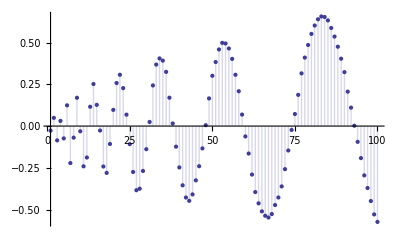

```mathematica
DiscretePlot[Re[ eedz[40 n, N[ZetaZero[1]], 1]],{n,1,100}]
```

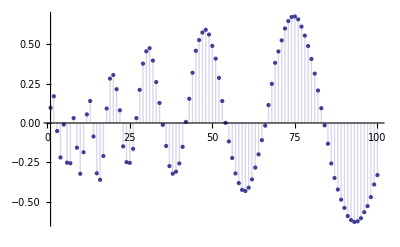

```mathematica
DiscretePlot[Im[ eedz[40 n, N[ZetaZero[1]], 1]],{n,1,100}]
```

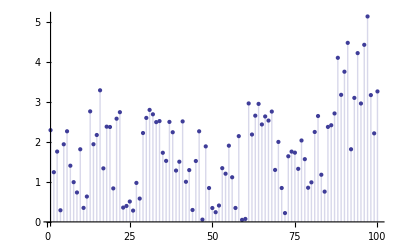

```mathematica
DiscretePlot[Abs[ altz[30 n, N[ZetaZero[1]], 1]],{n,1,100}]
```

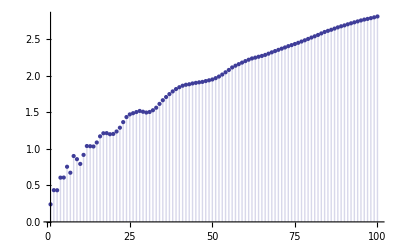

```mathematica
DiscretePlot[Abs[ dee[30 n, N[ZetaZero[1]], 1]],{n,1,100}]
```

```mathematica
edz[10000, N[ZetaZero[1]], 1]
```

-5.10324-0.798884 ⅈ

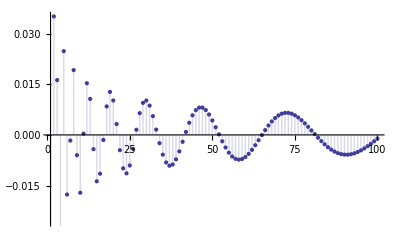

```mathematica
DiscretePlot[Re[ eedoz[80 n, N[ZetaZero[1]], 1]],{n,1,100}]
```

```mathematica
N@((eedz[10000,0,z]+eedz[10000,0,-z])/2)/.z->I+2Pi I
```

57548.2+0. ⅈ

```mathematica
Sum[ z^k / k!x^(-s k),{k,0,Infinity}]
```

ⅇ^(x^-s z)

```mathematica
N[(ⅇ^(x^-s z)+ⅇ^(x^-s (-z)))/2/.x->2/.z->2I/.s->2]
```

0.877583+0. ⅈ

```mathematica
Product[ ⅇ^(x^-2),{x,sdf}]
```

ⅇ^HarmonicNumber[sdf,2]

```mathematica
Log[ⅇ^(x^-s z)]
```

Log[ⅇ^(x^-s z)]

```mathematica
N@dee[1000000.,1.1,1]
```

6.40688

```mathematica
FullSimplify[Expand[(1/(s-1))(n/(n+1)^s-(n-s)/n^s)]]
```

(n (1+n)^-s+n^-s (-n+s))/(-1+s)

```mathematica
Table[dez[n,1],{n,1,100}]
```

{1,1,1,1/2,1,1,1,1/6,1/2,1,1,1/2,1,1,1,1/24,1,1/2,1,1/2,1,1,1,1/6,1/2,1,1/6,1/2,1,1,1,1/120,1,1,1,1/4,1,1,1,1/6,1,1,1,1/2,1/2,1,1,1/24,1/2,1/2,1,1/2,1,1/6,1,1/6,1,1,1,1/2,1,1,1/2,1/720,1,1,1,1/2,1,1,1,1/12,1,1,1/2,1/2,1,1,1,1/24,1/24,1,1,1/2,1,1,1,1/6,1,1/2,1,1/2,1,1,1,1/120,1,1/2,1/2,1/4}

```mathematica
PrimeQ[11]
```

True

```mathematica
is2[2]
```

```mathematica
FullSimplify[is2[32]]
```

32/5

```mathematica
N@D[dee[10000,0,z],{z,0}]
```

1.+1229. z+2612.5 z^2+2181.83 z^3+957.167 z^4+263.317 z^5+45.5958 z^6+5.49762 z^7+0.4313 z^8+0.0216049 z^9+0.000857859 z^10+9.11897×10^-6 z^11+1.64926×10^-7 z^12+1.6059×10^-10 z^13

```mathematica
PrimePi[10000]
```

1229

```mathematica
D[E^(z PrimeZetaP[s]),{z,4}]
```

ⅇ^(z PrimeZetaP[s]) PrimeZetaP[s]^4

```mathematica
ff[z_,s_]:=(E^z PrimeZetaP[s]+E^-z PrimeZetaP[s])/2
```

```mathematica
N@ff[2Pi I + 2I,2]
```

-0.188201+0. ⅈ

```mathematica
N@(dee[10000,2,2I+2Pi I]+dee[10000,2,-2I-2Pi I])/2
```

-0.827469-1.66533×10^-16 ⅈ

```mathematica
N@(dee[1000000,2,2I])
```

0.618082+0.786113 ⅈ

```mathematica
N@E^((I+2Pi I) PrimeZetaP[2])
```

-0.988439-0.151622 ⅈ

```mathematica
N@Expand@deee[1000000,2,z]
```

1.+0.452247 z+0.102264 z^2+0.015416 z^3+0.00174283 z^4+0.000157587 z^5+0.0000118633 z^6+7.63386×10^-7 z^7+4.26769×10^-8 z^8+2.08783×10^-9 z^9+8.90975×10^-11 z^10+3.28881×10^-12 z^11+1.02193×10^-13 z^12+2.64664×10^-15 z^13+5.2449×10^-17 z^14+8.31974×10^-19 z^15+9.13858×10^-21 z^16+6.50551×10^-23 z^17+3.11317×10^-25 z^18+2.8245×10^-28 z^19

```mathematica
(deee[1000000,2,I]+deee[1000000,2,-I])/2
```

$Aborted

```mathematica
v100[z_]:=1.+0.4522473522653741 z+0.10226367184134524 z^2+0.015415962433582885 z^3+0.001742831515174532 z^4+0.00015758654321969503 z^5+0.000011863275725862476 z^6+7.633863778094078*^-7 z^7+4.267692925500261*^-8 z^8+2.087828092466002*^-9 z^9+8.909746884969071*^-11 z^10+3.288807673239177*^-12 z^11+1.0219293646832407*^-13 z^12+2.6466413005396524*^-15 z^13+5.244896831849439*^-17 z^14+8.319743442894546*^-19 z^15+9.138584423399247*^-21 z^16+6.505508494609741*^-23 z^17+3.113170534545376*^-25 z^18+2.8245024763158775*^-28 z^19
```

```mathematica
(v100[I]+v100[-I])/2
```

0.899467+0. ⅈ

```mathematica
(v100[I+2Pi I]+v100[-I-2Pi I])/2
```

-0.988635+0. ⅈ

```mathematica
N[PrimeZetaP[2]]
```

0.452247

```mathematica
gf[x_,t_]:=Sum[ dez[k,1]x^k,{k,1,t}]
gf2[x_,t_]:=(x (-1+x^t))/(-1+x)
```

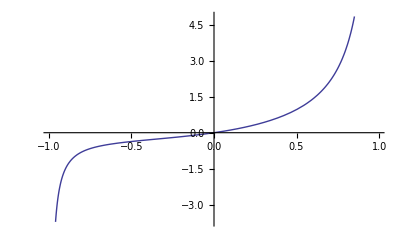

```mathematica
Plot[gf[x,10000],{x,-.99,.99}]
```

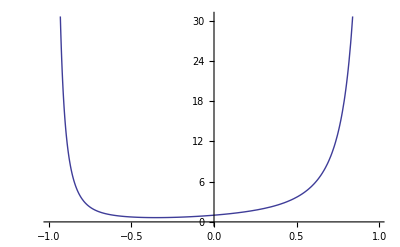

```mathematica
Plot[D[gf[x,10000],x]/.x->y,{y,-.99,.99}]
```

```mathematica
Table[ N@D[gf[x,10000],x]/.x->.5^k, {k,1,10}]
```

{3.67685,1.74605,1.30221,1.13729,1.0655,1.03199,1.01581,1.00786,1.00392,1.00196}

```mathematica
Table[ gf[.5^k,10000], {k,1,10}]
```

{0.964379,0.331366,0.142735,0.066659,0.0322576,0.015873,0.00787401,0.00392157,0.00195695,0.000977517}

```mathematica
Sum[ x^k,{k,1,t}]
```

(x (-1+x^t))/(-1+x)

```mathematica
rootsa[1000000,2]
```

{-877.729,-71.1618,-37.3299-96.7985 ⅈ,-37.3299+96.7985 ⅈ,-11.2549,-10.813-4.36228 ⅈ,-10.813+4.36228 ⅈ,-9.53977-8.79402 ⅈ,-9.53977+8.79402 ⅈ,-8.22574-43.3573 ⅈ,-8.22574+43.3573 ⅈ,-7.71922-13.0623 ⅈ,-7.71922+13.0623 ⅈ,-4.11337-16.6111 ⅈ,-4.11337+16.6111 ⅈ,-1.44157-19.9597 ⅈ,-1.44157+19.9597 ⅈ,8.15454-17.9539 ⅈ,8.15454+17.9539 ⅈ}

```mathematica
deee[1000,2,z]
```

1.+0.45212 z+0.101999 z^2+0.0151986 z^3+0.00165117 z^4+0.000133422 z^5+7.92725×10^-6 z^6+2.84793×10^-7 z^7+7.91626×10^-9 z^8+5.25614×10^-11 z^9

```mathematica
deee[1000,1,z]
```

1.+2.19808 z+1.81743 z^2+0.769749 z^3+0.191547 z^4+0.0288456 z^5+0.00280736 z^6+0.000129318 z^7+5.40495×10^-6 z^8+3.7676×10^-8 z^9

```mathematica
deee[1000,0,z]
```

1.+168 z+293.5 z^2+189.667 z^3+64.7083 z^4+12.225 z^5+1.48333 z^6+0.0710317 z^7+0.00409226 z^8+0.0000275573 z^9

```mathematica
deee[1000,-1,z]
```

1.+76127. z+144479. z^2+99082.3 z^3+36544.8 z^4+7368.42 z^5+979.729 z^6+44.1754 z^7+3.32063 z^8+0.0204586 z^9

```mathematica
E^(p^1 z) / E^(p^2 z)
```

ⅇ^(p z-p^2 z)

```mathematica
pz[s_,t_]:= Product[ Zeta[k s]^(MoebiusMu[k]/k),{k,1,t}]
```

```mathematica
Table[ N@pz[-3.17+I,2^k],{k,1,8}]
```

Power::indet: Indeterminate expression (0.  + 0.\ ⅈ)^0
 encountered.

{0.0123534+0.0873678 ⅈ,0.104733+0.0711296 ⅈ,0.0202845-0.00777074 ⅈ,2.1727-0.765559 ⅈ,9.541×10^-9-4.45087×10^-9 ⅈ,106.345-101.955 ⅈ,0.0128624-0.0138756 ⅈ,Indeterminate}

```mathematica
Table[ Zeta[k (-3.17+I)]^(MoebiusMu[k]/k),{k,200,200}]//TableForm
```

Power::indet: Indeterminate expression (0.  + 0.\ ⅈ)^0
 encountered.

Indeterminate

```mathematica
Expand[E^(a^b)]
```

```mathematica
2^-2
```

1/4

```mathematica
Table[deee[n,0,1]/n,{n,1000,100000,1000}]
```

{0.730658,0.730059,0.729808,0.729799,0.729808,0.729516,0.729492,0.729547,0.729519,0.729636,0.729457,0.729394,0.729465,0.729433,0.729482,0.729436,0.72952,0.729457,0.729452,0.72944,0.729441,0.729472,0.72939,0.729468,0.729368,0.729434,0.729311,0.729377,0.729346,0.729398,0.729415,0.729333,0.72932,0.729401,0.729363,0.729359,0.729358,0.729299,0.729297,0.729303,0.729322,0.729321,0.729378,0.72941,0.729384,0.729389,0.729425,0.729437,0.729396,0.72936,0.729382,0.729385,0.729369,0.729335,0.72936,0.729341,0.729336,0.729337,0.729303,0.729318,0.729376,0.729376,0.729354,0.729338,0.729333,0.72934,0.729334,0.729363,0.729316,0.729339,0.729346,0.729352,0.729346,0.729309,0.729313,0.729292,0.729298,0.729315,0.729321,0.729291,0.72929,0.729264,0.729299,0.729295,0.72931,0.729302,0.729304,0.729322,0.729342,0.729313,0.729312,0.729328,0.729348,0.729348,0.72934,0.729331,0.729323,0.729318,0.729303,0.72931}

```mathematica
N[dee[1000000,0,1]/1000000]
```

0.729276

```mathematica
N[deee[10000000,0,1]/10000000]
```

0.729268

```mathematica
N[deee[100000000,0,1]/100000000]
```

0.729266

```mathematica
Integrate[ E^(x),x]
```

ⅇ^x

```mathematica
D[E^x,x]
```

ⅇ^x

```mathematica
Table[dez[n,z],{n,1,40}]
```

{1,z,z,z^2/2,z,z^2,z,z^3/6,z^2/2,z^2,z,z^3/2,z,z^2,z^2,z^4/24,z,z^3/2,z,z^3/2,z^2,z^2,z,z^4/6,z^2/2,z^2,z^3/6,z^3/2,z,z^3,z,z^5/120,z^2,z^2,z^2,z^4/4,z,z^2,z^2,z^4/6}

```mathematica
dee[100,0,z]
```

1+25 z+32 z^2+(77 z^3)/6+(35 z^4)/12+(7 z^5)/40+(7 z^6)/720

```mathematica
Expand@Sum[ dez[j,1] dee[100/j,0,z-1],{j,1,100}]
```

1+25 z+32 z^2+(77 z^3)/6+(35 z^4)/12+(7 z^5)/40+(7 z^6)/720

```mathematica
Expand@Sum[ dez[j,1] dez[k,z-1],{j,1,100},{k,1,100/j}]
```

1+25 z+32 z^2+(77 z^3)/6+(35 z^4)/12+(7 z^5)/40+(7 z^6)/720